# Rot3

Taylor Expansion in Logmap

```mathematica
Series[t/(2 Sin[t]),{t,0,3}]
```

1/2+t^2/12+O[t]^4

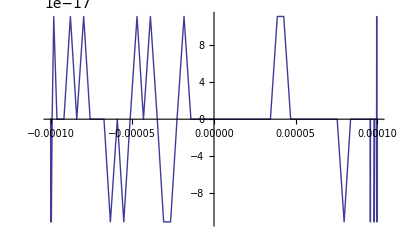

```mathematica
Plot[1/2+t^2/12-t/(2 Sin[t]),{t,-10^-4,10^-4}]
```

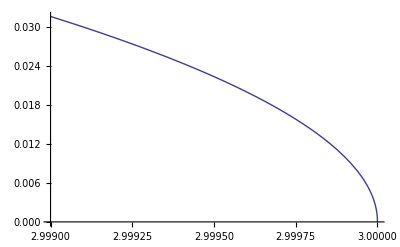

```mathematica
Plot[ArcCos[(t-1)/2],{t,2.999,3}]
```

```mathematica
exp=ArcCos[(t-1)/2]/(2 Sin[ArcCos[(t-1)/2]])//Simplify
```

ArcCos[1/2 (-1+t)]/(√(3+2 t-t^2))

```mathematica
Series[exp,{t,3,1}]
```

(-1)^Floor[-Arg[-3+t]/(2 π)] (1/2-(t-3)/12+O[t-3]^2)

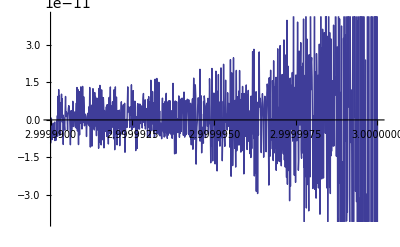

```mathematica
Plot[{exp-(1/2-(t-3)/12)},{t,3-10^-5,3}]
```

```mathematica
FullSimplify[(2*Sin[t]-t*(1+Cos[t]))/(2*Sin[t])]//CForm
```

1 - (t*Cot(t/2.))/2.

## Cayley Transform in retract

```mathematica
Skew[xi_,yi_,zi_]:=({{0, -zi, yi}, {zi, 0, -xi}, {-yi, xi, 0}})
```

```mathematica
I3=IdentityMatrix[3];
```

```mathematica
Cayley[A_]:=(I3-A).Inverse[I3+A]
```

```mathematica
Cayley[-({{0, -z, y}, {z, 0, -x}, {-y, x, 0}})/2]//Simplify
```

{{(4+x^2-y^2-z^2)/(4+x^2+y^2+z^2),(2 x y-4 z)/(4+x^2+y^2+z^2),(4 y+2 x z)/(4+x^2+y^2+z^2)},{(2 x y+4 z)/(4+x^2+y^2+z^2),(4-x^2+y^2-z^2)/(4+x^2+y^2+z^2),(2 (-2 x+y z))/(4+x^2+y^2+z^2)},{(2 (-2 y+x z))/(4+x^2+y^2+z^2),(4 x+2 y z)/(4+x^2+y^2+z^2),(4-x^2-y^2+z^2)/(4+x^2+y^2+z^2)}}

## Inverse Cayley Transform in localCoordinates

```mathematica
Cayley[({{a, b, c}, {d, e, f}, {g, h, i}})]//Simplify//MatrixForm
```

((1+e+c g+c e g-c d h-f h+i+e i+b (d-f g+d i)-a (1+e-f h+i+e i))/(1+e-c g-c e g+c d h-f h+i+e i-b (d-f g+d i)+a (1+e-f h+i+e i)) | -(2 (b-c h+b i))/(1+e-c g-c e g+c d h-f h+i+e i-b (d-f g+d i)+a (1+e-f h+i+e i)) | -(2 (c+c e-b f))/(1+e-c g-c e g+c d h-f h+i+e i-b (d-f g+d i)+a (1+e-f h+i+e i))
-(2 (d-f g+d i))/(1+e-c g-c e g+c d h-f h+i+e i-b (d-f g+d i)+a (1+e-f h+i+e i)) | (1-e-c g+c e g-c d h+f h+i-e i+b (d-f g+d i)+a (1+f h+i-e (1+i)))/(1+e-c g-c e g+c d h-f h+i+e i-b (d-f g+d i)+a (1+e-f h+i+e i)) | -(2 (-c d+f+a f))/(1+e-c g-c e g+c d h-f h+i+e i-b (d-f g+d i)+a (1+e-f h+i+e i))
-(2 (g+e g-d h))/(1+e-c g-c e g+c d h-f h+i+e i-b (d-f g+d i)+a (1+e-f h+i+e i)) | -(2 (-b g+h+a h))/(1+e-c g-c e g+c d h-f h+i+e i-b (d-f g+d i)+a (1+e-f h+i+e i)) | (1+e+c g+c e g-c d h+f h-i-e i-b (d+f g-d i)+a (1+e+f h-i-e i))/(1+e-c g-c e g+c d h-f h+i+e i-b (d-f g+d i)+a (1+e-f h+i+e i)))

```mathematica
FullSimplify[1+e-c g-c e g+c d h-f h+i+e i-b (d-f g+d i)+a (1+e-f h+i+e i)]/.{1+e-f h+i+e i->K}
```

-c (1+e) g+c d h-b (d-f g+d i)+a (1+e-f h+i+e i)+K